```mathematica
(*FUNCTION DEFINITION*)
variables = {Bmax,Y0,Kd,x};
(*f=Function[Evaluate@variables,(*YOUR FUNCTION HERE*)];*)
f=Function[Evaluate@variables,(Bmax-Y0)*x/(x+Kd)+Y0];

tab={Table[Subscript[c, i],{i,1,Length[variables]}]}//Flatten;
table=Table[(D[f @@tab,Subscript[c, i]]*Subscript[σ, Subscript[c, i]])^2,{i,1,Length[variables]}]/.Table[tab[[i]]->variables[[i]],{i,Length[variables]}];
sigmaf[X_]:=Sqrt[Sum[table[[i]],{i,1,Length[variables]}]]/.{x->X}
ttest=Abs[(((f@@variables/.x->α x)-(f@@variables/.x-> x))/Sqrt[sigmaf[α x]^2+sigmaf[x]^2])/.Subscript[σ, α x]-> Subscript[σ, x]];
```

```mathematica
calculateResolution[values_,errors_]:=
Module[{},{
substitution1=Table[Subscript[σ, variables[[i]]]->errors[[i]],{i,Length[variables]}];
substitution2=Table[variables[[i]]->values[[i]],{i,Length[variables]}];

sol=Solve[(ttest/.substitution1/.substitution2)==4.5/Sqrt[3]&&α>1&&x>0,α];

xmin = -3;xmax = 2;s=10;
CI = 1.645;(*90% 1.645, 95% 1.960, 99% 2.576, 99.5% 2.807*)
Plot[{(f@@values)/.x->10^X,(f@@values+CI*sigmaf[x]/.substitution1/.substitution2)/.x->10^X,(f@@values-CI*sigmaf[x]/.substitution1/.substitution2)/.x->10^X,α/10/.sol/.x->10^X},{X,xmin,xmax},AxesOrigin->{xmin,0}],
FindMinimum[α/.sol/.x->10^X,{X,Log10[values[[3]]]}],
Plot[{(f@@values)/.x->10^X,((sigmaf[x]/.substitution1/.substitution2)/.x->10^X)/D[(f@@values)/.x->10^x,x]/.x->X},{X,xmin,xmax}],
alphas=Table[{10^(i/s)//N,α/.sol/.x->10^(i/s)},{i,s*xmin,s*xmax}]//MatrixForm,
scale=1.05;
α/.sol/.x->0.4}];

(*LOD CALCULATION*)
calculateLOD[values_,errors_]:=
Module[{},
variablesinv = {Bmax,Y0,Kd,y};
temp=x/.Solve[f@@variables==y,x][[1]];
finv=Function[Evaluate@variablesinv,(Kd (y-Y0))/(Bmax-y)];
tabinv={Table[Subscript[c, i],{i,1,Length[variables]}]}//Flatten;
tableinv=Table[(D[finv @@tabinv,Subscript[c, i]]*Subscript[σ, Subscript[c, i]])^2,{i,1,Length[variables]}]/.Table[tabinv[[i]]->variablesinv[[i]],{i,Length[variables]}];
sigmafinv[errs_,vals_]:=(Sqrt[Sum[tableinv[[i]],{i,1,Length[vals]}]]/.Table[Subscript[σ, variablesinv[[i]]]->errs[[i]],{i,Length[vals]}]/.Table[variablesinv[[i]]->vals[[i]],{i,Length[vals]}])/.y->vals[[Length[vals]]];
{finv @@ values,"+/-",sigmafinv[errors,values]}//MatrixForm
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

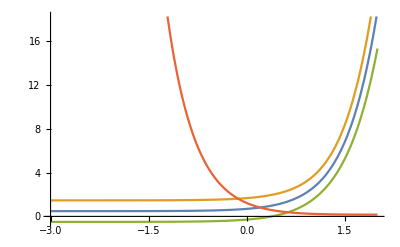
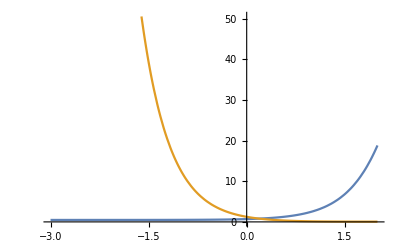
{-Graphics-,{1.62878,{X→2.05827}},-Graphics-,{1860.72}}

```mathematica
(*Qorvo (Direct)*)values={147.735236497151,0.481010101819776,704.074470831177,x};errors={7.91475045804365,0.598021661621242,77.7357123703907,0};calculateResolution[values,errors]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

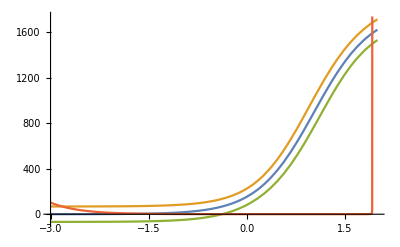
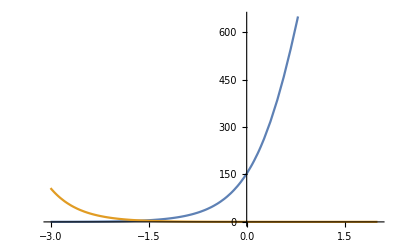
{-Graphics-,{1.86689,{X→0.827873}},-Graphics-,{171.774}}

```mathematica
(*Qorvo (Enzyme)*)values={1796.43776294984,8.16939188409543*10^-06,10.7477090570673,x};errors={55.2021021327212,41.1713554955947,1.65225707537587,0};calculateResolution[values,errors]
```

```mathematica
8.16939188409543E-06
```

16.2067